```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=20;
Ly=20;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM[t_,t0_,m_,tz_,kz_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[2*Cons-t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM[1.,1.,4,1,π/2-0.5,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

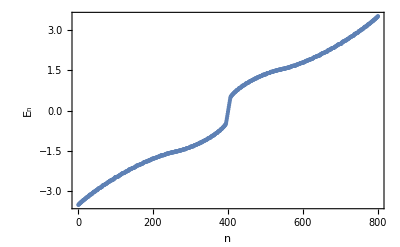

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],(**Plot[0,{x,0,2A},PlotStyle-> Red],**)BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,50]
```

{-3.14159,-3.01593,-2.89027,-2.7646,-2.63894,-2.51327,-2.38761,-2.26195,-2.13628,-2.01062,-1.88496,-1.75929,-1.63363,-1.50796,-1.3823,-1.25664,-1.13097,-1.00531,-0.879646,-0.753982,-0.628319,-0.502655,-0.376991,-0.251327,-0.125664,0.,0.125664,0.251327,0.376991,0.502655,0.628319,0.753982,0.879646,1.00531,1.13097,1.25664,1.3823,1.50796,1.63363,1.75929,1.88496,2.01062,2.13628,2.26195,2.38761,2.51327,2.63894,2.7646,2.89027,3.01593,3.14159}

```mathematica
aaaaa=Dimensions[kzVector][[1]]
```

51

```mathematica
(**OBC**)
```

```mathematica
(* Clear[b];
b={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM[1.,1.,4,1,kzVector[[i]],0]],
Do[b=Append[b,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,aaaaa}] *)
```

```mathematica
(* ListPlot[b] *)
```

```mathematica
(**PBC**)
```

```mathematica
(*Clear[bb];
bb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM[1.,1.,4,1,kzVector[[i]],1]],
Do[bb=Append[bb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,aaaaa}]*)
```

```mathematica
(*ListPlot[bb]*)
```

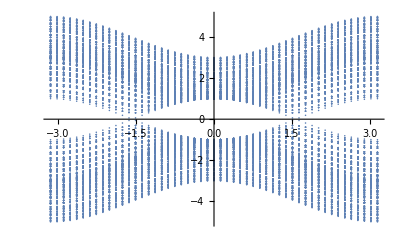

-Graphics-

```mathematica
(**----Clear memory for quasicrystal----**)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

800

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+4
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+2
```

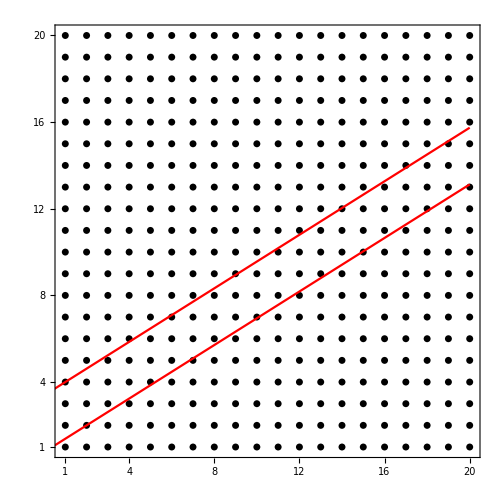

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy, P,U,V,LogEigenValuesBott,Bott, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{21,41,42,43,62,63,64,65,83,84,85,86,105,106,107,108,126,127,128,129,130,148,149,150,151,170,171,172,173,191,192,193,194,213,214,215,216,234,235,236,237,238,256,257,258,259,278,279,280,299,300}

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{41,42,81,82,83,84,85,86,123,124,125,126,127,128,129,130,165,166,167,168,169,170,171,172,209,210,211,212,213,214,215,216,251,252,253,254,255,256,257,258,259,260,295,296,297,298,299,300,301,302,339,340,341,342,343,344,345,346,381,382,383,384,385,386,387,388,425,426,427,428,429,430,431,432,467,468,469,470,471,472,473,474,475,476,511,512,513,514,515,516,517,518,555,556,557,558,559,560,597,598,599,600}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

102

```mathematica
NOrbitalsQuasi/2
```

51

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

698

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.1275

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{800}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(**-------------------------------**)
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2}];
```

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

39

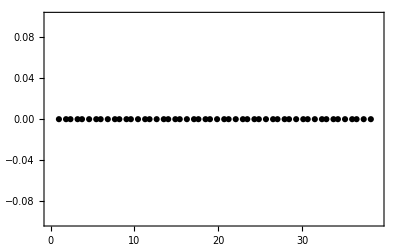

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
(**-------------------------------**)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[TabFibNew, TabRenorEnergies]
```

```mathematica
TabFibNew={}
```

{}

```mathematica
TabRenorEnergies={}
```

{}

```mathematica
Do[{Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
HTrial=HamiltonianWSM[1.,1.,4,1,kzVector[[p]],1],
(*---------------------------------------------------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}],
(*---------------------------------------------------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------------------------------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}],
(*-------------------------------------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon],
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB),
(**------Check that HFibonRenor is Hermitian------**)
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor],
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First],
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop,
(*Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black(**,PlotRange->{{0,84},{-2,2}}**)],Plot[0,{x,-100,100},PlotStyle-> Red]]*)
(** without dislocation -1 OBC **)
(** without dislocation +1 OBC **)
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsQuasi}],
Tr[OnlyEigenvalue]//Chop,
percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)],
NSitesInside = NOrbitalsQuasi/2,
(*---------------------------------------------------------------------------------------------------------*)
(*---------------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------------------------------------------*)
ValFibon[[(NOrbitalsQuasi/2)+1,2]],
Clear[J,TabDataFibon,TDFibon],
J=NOrbitalsQuasi/2;,
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,i]]]^2+Abs[ValVecFibon[[J,2,i+NOrbitalsQuasi/2]]]^2

+Abs[ValVecFibon[[J+1,2,i]]]^2+Abs[ValVecFibon[[J+1,2,i+NOrbitalsQuasi/2]]]^2

},{i,1,NOrbitalsQuasi/2}],
TDFibon=Flatten[TabDataFibon],
Do[TabFibNew = Append[TabFibNew,{TDFibon[[i]],kzVector[[p]],TDFibon[[i+2]]}],{i,1,3*NOrbitalsQuasi/2,3}],
Do[TabRenorEnergies = Append[TabRenorEnergies,{kzVector[[p]],OnlyEigenvalue[[i]]}],{i,1,NOrbitalsQuasi}]
},{p,1,aaaaa}]
```

```mathematica
(* TabFibNew=Import["/home/archisman/Documents/GitHub/quasicrystals/results/WSM/OBC/one-set-data/WSM-high-occ-density.dat"]; *)
```

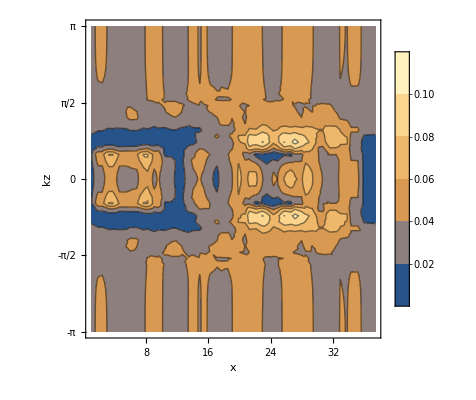

```mathematica
P33=ListContourPlot[TabFibNew,PlotRange->All, FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,FrameLabel-> {"x","kz"},FrameTicks->{{{-π,-π/2,0,π/2,π},None},{Automatic,None}},PlotLegends->Automatic]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@TabFibNew[[All,3]];
```

```mathematica
rng[[2]]
```

0.106246

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.076"},{rng[[2]]-10^-3,"0.152"}}]
```

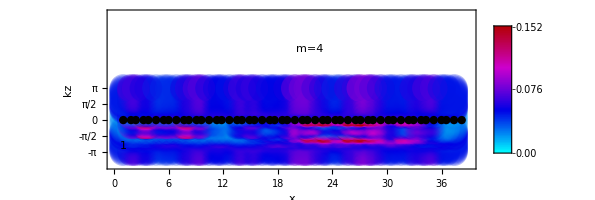

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNew,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX},{-4.5,10.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
FrameTicks->{{{-π,-π/2,0,π/2,π},None},{Automatic,None}},FrameLabel-> {"x","kz"},
Epilog-> {Inset[1,{1,-2.5}],
Rotate[Inset[P1,{11,7.00}],90 Degree],Inset["m=4",{21.5,7}]
(* ,Inset["(a)",{1.25,7}]*)
}
]
```

```mathematica
(* Export["/home/archisman/Documents/GitHub/quasicrystals/results/WSM/PBC/one-set-data/WSM-high-occ-density.dat",TabFibNew]; *)
```

```mathematica
(***---- Calculation of energy eigenvalues for different kz---***)
```

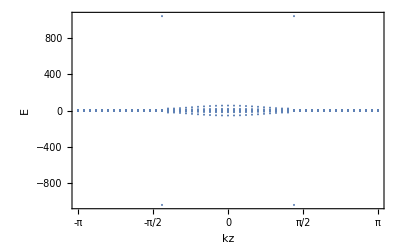

```mathematica
ListPlot[TabRenorEnergies,Frame->True,FrameStyle-> Black,
BaseStyle-> 18,FrameLabel->{"kz","E"},FrameTicks->{Automatic,{{-π,-π/2,0,π/2,π},None}},PlotRange->All]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

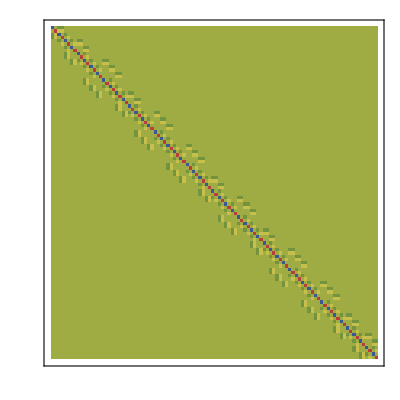

```mathematica
ArrayPlot[Re[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

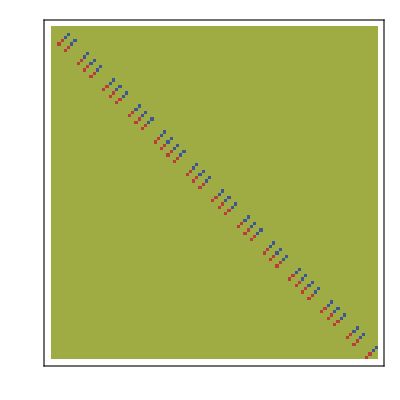

```mathematica
ArrayPlot[Im[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

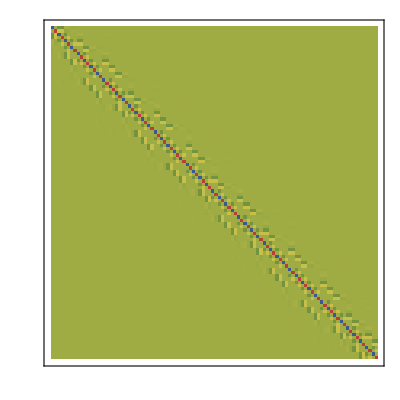

```mathematica
ArrayPlot[Re[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

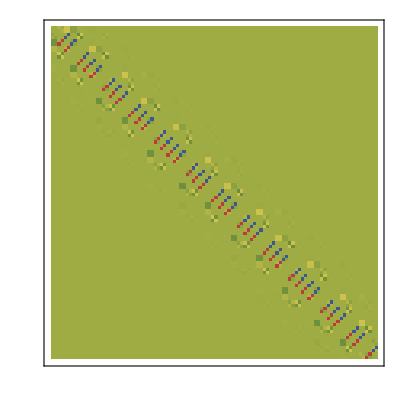

```mathematica
ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```